# Projection onto the (κ, y) plane of the phase trajectory in the Stirling cycle

```mathematica
ClearAll["Global`*"]
```

```mathematica
<<MaTeX`
```

## Cycle parameters

```mathematica
χ=0.5;ν=0.5;
kA=1; yA=1;θA=1;
kB= χ; yB=1/χ;θB=1;
kC=χ; yC=ν/χ;θC=ν;
kD=1; yD=ν;θD=ν;
```

```mathematica
Wqs[ν_,χ_]:=(1-ν)/2 Log[χ];
A[χ_]:=(1/(√χ)-1)^2;
w[ν_,χ_]:=(-Wqs[ν,χ])/(A[χ]*(1+√ν)^2);
tisoc[ν_,χ_]:=-1/(2χ)Log[ν];
σ[ν_,χ_]:=√(1+w[ν,χ]*tisoc[ν,χ]);
sAB[ν_,χ_]:=(1+σ[ν,χ])/(w[ν,χ]*(1+√ν));
sCD[ν_,χ_]:=√ν*sAB[ν,χ];
WAB[ν_,χ_]:=Log[χ]/2+A[χ]/sAB[ν,χ];
WCD[ν_,χ_]:=(-ν*Log[χ])/2+(ν*A[χ])/sCD[ν,χ];
P[ν_,χ_]:=-(WAB[ν,χ]+WCD[ν,χ])/(sAB[ν,χ]+sCD[ν,χ]+tisoc[ν,χ]);
η[ν_,χ_]:=1+WCD[ν,χ]/WAB[ν,χ];
ηC[ν_]:=1-ν;
ηCA[ν_]:=1-√ν;
```

## Auxiliary plotting functions

```mathematica
th = 0.008;magnif = 2;
```

```mathematica
PlotPoint[k_,y_,color_]:=Graphics[{color,PointSize[0.025],Point[{k,y}]}];
```

```mathematica
FontSizeFactor = 0.9;writeAqs=Graphics[Text[Style[MaTeX["A",Magnification->FontSizeFactor*magnif]],{kA+Δtext,yA+Δtext}],Automatic,{1,0}];writeBqs =Graphics[Text[Style[MaTeX["B",Magnification->FontSizeFactor*magnif]],{kB-Δtext,yB+Δtext}],Automatic,{1,0}];writeCqs =Graphics[Text[Style[MaTeX["C",Magnification->FontSizeFactor*magnif]],{kC-Δtext,yC-3*Δtext}],Automatic,{1,0}];writeDqs=Graphics[Text[Style[MaTeX["D",Magnification->FontSizeFactor*magnif]],{kD+Δtext,yD-Δtext}],Automatic,{1,0}];
writeAirrev=Graphics[Text[Style[MaTeX["A",Magnification->FontSizeFactor*magnif]],{kA+Δtext,yA+Δtext}],Automatic,{1,0}];writeBirrev =Graphics[Text[Style[MaTeX["B",Magnification->FontSizeFactor*magnif]],{kB+Δtext,yB+Δtext}],Automatic,{1,0}];writeCirrev =Graphics[Text[Style[MaTeX["C",Magnification->FontSizeFactor*magnif]],{kC-Δtext,yC-Δtext}],Automatic,{1,0}];writeDirrev=Graphics[Text[Style[MaTeX["D",Magnification->FontSizeFactor*magnif]],{kD-Δtext,yD-Δtext}],Automatic,{1,0}];
```

```mathematica
LTicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,NumberForm[x,{2,1}, NumberPadding -> {"","0"}],{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];

STicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,"",{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];
```

## Isochoric branches

```mathematica
PlotISOC[k_,y0_,yf_]:=ParametricPlot[{k,y},{y,y0,yf},ColorFunction->(Blend[{Blue,Red},#2]&),PlotStyle->Thickness[th]];
```

## Isothermal branches

### Quasi-static cycle

```mathematica
PlotISOTqs[y0_,k0_,kf_,color_]:=Plot[(y0*k0)/k,{k,k0,kf},PlotRange->All,PlotStyle->{color,Thickness[th]}];
```

### Irreversible cycle

```mathematica
yISOT[y0_,yf_,sf_,s_]:=(Sqrt[y0]+(Sqrt[yf]-Sqrt[y0])s/sf)^2;
kISOT[T_,y0_,yf_,sf_,s_]:=T/yISOT[y0,yf,sf,s]-1/2 D[yISOT[y0,yf,sf,t],t]/.t->s;
PlotISOT[T_,y0_,yf_,sf_,color_]:=ParametricPlot[{kISOT[T,y0,yf,sf,s],yISOT[y0,yf,sf,s]},{s,0,sf},PlotRange->All,PlotStyle->{color,Thickness[th]}];
PlotJump[k0_,y0_,kf_,yf_,color_]:=ListLinePlot[{{k0,y0},{kf,yf}},PlotRange->All,PlotStyle->{color,Dashed}];
JumpA=PlotJump[kA,yA,kISOT[θA,yA,yB,sAB[ν,χ],0],yA,Red];
JumpB=PlotJump[kB,yB,kISOT[θA,yA,yB,sAB[ν,χ],sAB[ν,χ]],yB,Red];
JumpC=PlotJump[kC,yC,kISOT[θC,yC,yD,sCD[ν,χ],0],yC,Blue];
JumpD=PlotJump[kD,yD,kISOT[θC,yC,yD,sCD[ν,χ],sCD[ν,χ]],yD,Blue];
```

## Figure 2

### Quasi-static cycle

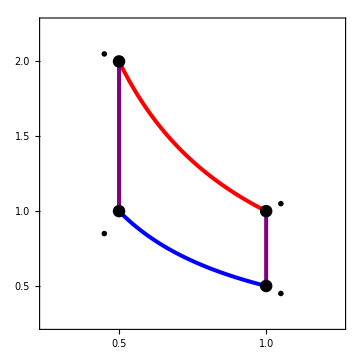

```mathematica
Δtext = 0.05;
xm=0;xM=1.5;Δxm=0.1;ΔxM=0.5;
ym=0;yM=3;Δym=0.2;ΔyM=0.5;
QsProjection=Show[PlotISOTqs[yA,kA,kB,Red],PlotISOTqs[yC,kC,kD,Blue],PlotISOC[kB,yB,yC],PlotISOC[kA,yA,yD],PlotPoint[kA,yA,Black],PlotPoint[kB,yB,Black],PlotPoint[kC,yC,Black],PlotPoint[kD,yD,Black],writeAqs,writeBqs,writeCqs,writeDqs,AspectRatio->1,PlotRange->{{0.25,1.25},{0.25, 2.25}},FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->False,
LabelStyle->Directive[Black,0.8*magnif,FontFamily->"Times New Roman"],RotateLabel->False,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Times New Roman",Thickness[0.6*th]],FrameLabel->{MaTeX["\\kappa",Magnification->magnif],MaTeX["y",Magnification->magnif]},Frame->True,ImageSize->Medium]
```

### Irreversible cycle

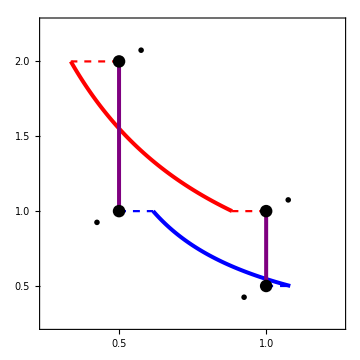

```mathematica
Δtext = 0.075;
xm=0;xM=1.5;Δxm=0.1;ΔxM=0.5;
ym=0;yM=3;Δym=0.2;ΔyM=0.5;
IrreveresibleProjection=Show[PlotISOT[θA,yA,yB,sAB[ν,χ],Red],PlotISOT[θC,yC,yD,sCD[ν,χ],Blue],PlotISOC[kB,yB,yC],PlotISOC[kA,yD,yA],JumpA,JumpB,JumpC,JumpD,PlotPoint[kA,yA,Black],PlotPoint[kB,yB,Black],PlotPoint[kC,yC,Black],PlotPoint[kD,yD,Black],writeAirrev,writeBirrev,writeCirrev,writeDirrev,AspectRatio->1,PlotRange->{{0.25,1.25},{0.25, 2.25}},FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->False,
LabelStyle->Directive[Black,10.8*magnif,FontFamily->"Times New Roman"],RotateLabel->False,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Times New Roman",Thickness[0.6*th]],FrameLabel->{MaTeX["\\kappa",Magnification->magnif],MaTeX["y",Magnification->magnif]},Frame->True,ImageSize->Medium]
```